更多可视化的形式

我们已经看到了如何使用 ListPlot 以及 ListLinePlot 来绘制数据列表。如果你想同时绘制几组数据，你只需把它们放在一个列表中。

同时绘制两组数据：

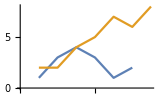

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}}]
```

PlotStyle 选项让你可以为每组数据指定样式：

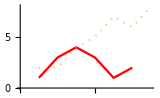

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}},PlotStyle->{Red,Dotted}]
```

Mesh 选项让你可以显示出实际的数据点：

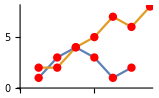

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}},Mesh->All,MeshStyle->Red]
```

除了查看列表中的数值序列外，想看看不同数值出现的频率也是很常见的。你可以用 Histogram 来做这个。

以下是前 30 个常见英语单词的长度：

```mathematica
StringLength[Take[WordList[ ],30]]
```

{1,3,8,5,6,5,7,7,9,11,5,9,5,7,9,5,9,8,4,6,5,5,10,11,12,8,10,7,9,6}

用直方图来显示出每个长度在前 200 个词中出现的频率：

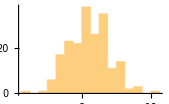

```mathematica
Histogram[StringLength[Take[WordList[ ],200]]]
```

将所有的单词包括在内，将会有一个更平滑的结果：

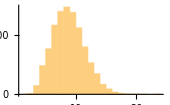

```mathematica
Histogram[StringLength[WordList[ ]]]
```

有时候，你会有一些你会想在三维中进行数据可视化。例如，GeoElevationData 将给出一个海拔值的数组。ListPlot3D 可以创建一个三维图。

找到在珠穆朗玛峰周围的海拔数据，并将其绘制成 3D 图：

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]]]
```

-Graphics3D-

如果不需要显示网格：

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]],MeshStyle->None]
```

-Graphics3D-

另一种可视化方法是等高线图，在这种情况下，人们实际上是从上面看，并在均匀的高度上画出等高线。

创建一个等高线图，其中连续的高度范围被等高线隔开：

```mathematica
ListContourPlot[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]]]
```

-Graphics-

当人们处理大量的数据时，通常最好使用更简单的可视化，比如地势图，它基本上只是根据高度来着色。

将珠穆朗玛峰周围 100 英里的地形绘制成浮雕图：

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]]]
```

-Graphics-

词汇

ListLinePlot[{list_1,list_2,...}] |   | 将多个列表绘制在一起
Histogram[list] |   | 创建一个直方图
ListPlot3D[array] |   | 以数组为高度在三维中进行绘制
ListContourPlot[array] |   | 以数组为高度绘制等高线
ReliefPlot[array] |   | 绘制地势图
GeoElevationData[region] |   | 获取指定区域的地理海拔数据
PlotStyle |   | 设置每组数据样式的选项
Mesh |   | 是否需要网格点或网格线
MeshStyle |   | 设置网格样式的选项

"共有 11 道习题"
"以及 1 道附加题" | "开始练习 »"

在一个图中绘制 10 以内的整数的平方、立方以及 4 次方曲线。»

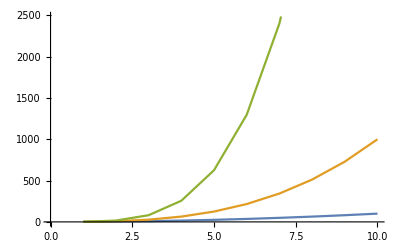
| 期望输出： |  
  | -Graphics- |

绘制前 20 个质数的图形，用一条线进行连接，填充到轴上，每个质数上有一个红点。»

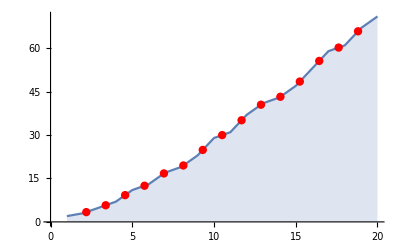
| 期望输出： |  
  | -Graphics- |

将富士山(Mount Fuji)周围 20 英里的地形绘制成三维图。»

| 期望输出： |  
  | -Graphics3D- |

将富士山(Mount Fuji)周围 100 英里的地形绘制成浮雕图。»

| 期望输出： |  
  | -Graphics- |

将 Mod[i,j] 生成的高度绘制成三维图，其中 i 和 j 最大为 100。»

| 期望输出： |  
  | -Graphics3D- |

将前 10000 个质数的连续质数之间的差值创建为直方图。»

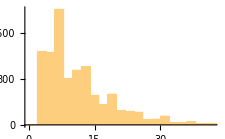
| 期望输出： |  
  | -Graphics- |

将 10000 以内的整数的平方值的首位数绘制为直方图(说明本福特定律)。»

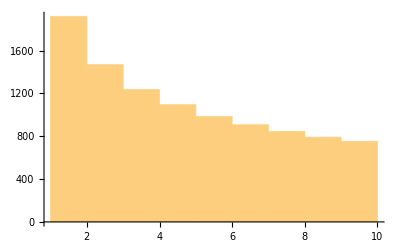
| 期望输出： |  
  | -Graphics- |

将 1000 以内的罗马数字的长度绘制为直方图。»

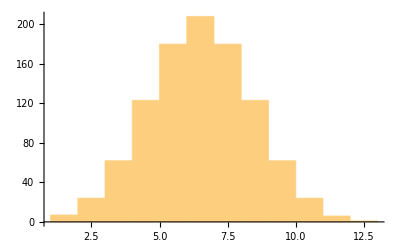
| 期望输出： |  
  | -Graphics- |

为维基百科上关于计算机的文章中的句子长度创建一个直方图。»

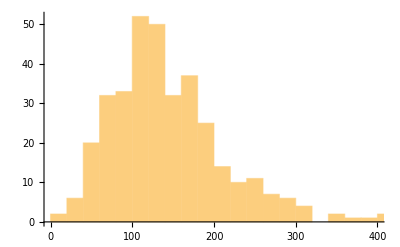
| 期望输出： |  
  | -Graphics- |

将 10000 个 100 以内的 n 个随机实数的和创建为直方图，其中 n 从 1 到 5(说明中心极限定理)。»

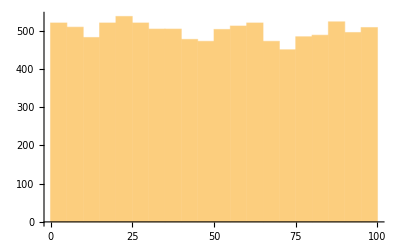
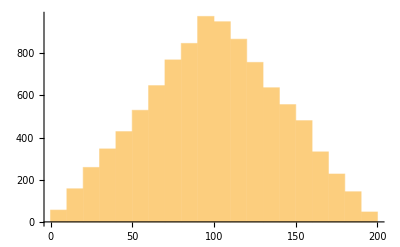
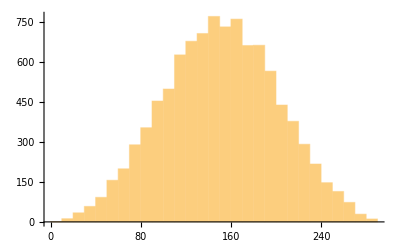
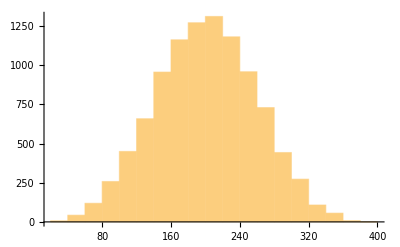
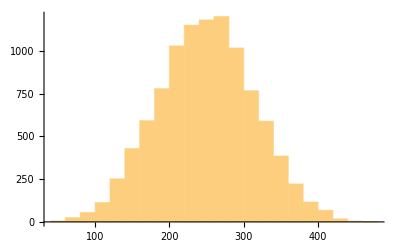
| 期望输出示例： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

使用二值化大小为 200 的字母 “W” 的图像数据作为高度，生成一个三维点集图。»

| 期望输出： |  
  | -Graphics3D- |

为维基百科上关于计算机的文章的单词长度创建一个直方图。»

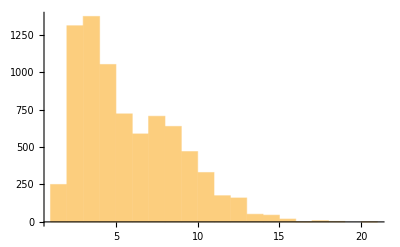
| 期望输出： |  
  | -Graphics- |

问&答

还有哪些其他的可视化类型？

还有非常多。比如 ListStepPlot 和 ListStreamPlot，或者 BubbleChart 和 BarChart3D，再比如 SmoothHistogram 以及 BoxWhiskerChart，或者 AngularGauge 以及 VerticalGauge。

如何合并我已经单独创建的图？

使用 Show 来将它们组合在共同的轴上。使用 GraphicsGrid (详见第 37 节)来把它们并排放在一起。

如何指定直方图中使用的直方条？

Histogram[list,n] 将使用 n 个直方条。Histogram[list,{x_min,x_max,dx}] 将在 x_min 到 x_max 的范围内使用宽度为 dx 的直方条。

条形图和直方图之间有什么区别？

条形图是数据的直接表示，而直方图表示数据出现的频率。在条形图中，每个直方条的高度给出了单个数据的值。在直方图中，每个直方条的高度给出了在直方条的范围 x 内出现的数据的总数。

如何在三维地形图上绘制等高线？
How can I draw contour lines on a 3D topography plot?

使用 MeshFunctions→(#3&)。(#3&) 是一个纯函数(详见第 26 节)，它使用第三个坐标(z)来创建网格。

如何在等高线图中标注高度？

使用 ContourLabels→All。

技术笔记

Wolfram 语言为可视化功能进行了许多自动选择。你可以用选项来覆盖这些选择。

使用 PlotStyle 的另一种方法是将 Style 直接插入到 ListLinePlot 等函数的数据中。

至少在地球的大部分地区，GeoElevationData 的数据测量分辨率可以达到 40 米左右。

探索更多

Wolfram 语言中的数据可视化指南 »